```mathematica
ChromaticPolynomial[ReadGrof[1318],4]/24
```

4

```mathematica
ChromaticPolynomial[Rule2[ReadGrof[205],5<->10,2<->7],4]/24
```

41

```mathematica
IsomorphicGraphQ[Rule2[ReadGrof[205],5<->10,2<->7],ReadGrof[1318]]
```

False

```mathematica
makeEges[list_]:=Sort/@UndirectedEdge@@@Partition[list,2,1]

(*FindFace:finds the smallest cycle.This cycle is a pseudo-face.*)
FindFace[graph_,edges_]:=MapAt[makeEges,First@SortBy[Transpose[{FindShortestPath[graph,Sequence@@#]&/@edges,edges}],Composition[Length,First]],1]

(*Append analyzed edge to a graph*)
appendEge[graph_,edge_]:=System`Graph@Append[EdgeList[graph],edge]

iteration[graph_,{}]:=$faces;

iteration[graph_,edges_]:=iteration[AppendTo[$faces,Flatten[#]];appendEge[graph,Last@#],DeleteCases[edges,Last@#]]&[FindFace[graph,edges]]

(*Faces:returns all pseudo-faces of a graph*)
NewFaces[graph_]:=Block[{$faces={},tree=FindSpanningTree[graph]},iteration[tree,Complement[EdgeList[graph],EdgeList[tree]]]]
```

```mathematica
OtherEdge[g_,d_]:=With[
{vert=DeleteDuplicates[DeleteCases[DeleteCases[Flatten[Map[{#[[1]],#[[2]]}&,Flatten[Select[NewFaces[g],MemberQ[#,d]||MemberQ[#,Reverse[d]]&]]]],d[[1]]],d[[2]]]]},
vert[[1]]<->vert[[2]]
]
```

```mathematica
With[
{g=ReadGrof[205]},
Table[e->ChromaticPolynomial[Rule2[g,e,OtherEdge[g,e]],4]/24,{e,EdgeList[g]}]
]
```

Part::partw: Part 2 of {10} does not exist.

Part::partw: Part 2 of {4} does not exist.

Part::partw: Part 2 of {3} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

{1<->2→14,1<->3→41,1<->7→14,1<->10→41,2<->3→6,2<->5→6,2<->9→25,2<->10→14,3<->4→10,3<->6→10,3<->7→6,3<->8→10,3<->9→10,4<->5→10,4<->6→25,4<->8→25,5<->6→10,5<->7→39,5<->8→57,5<->9→10,5<->10→41,6<->9→25,7<->8→87,7<->10→14}

Part::partw: Part 2 of {10} does not exist.

Part::partw: Part 2 of {4} does not exist.

Part::partw: Part 2 of {3} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

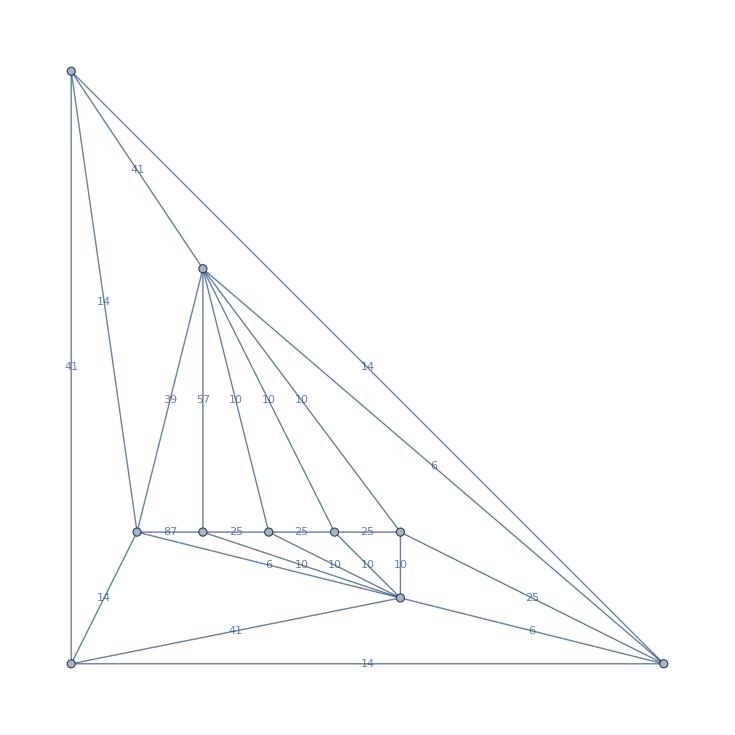

```mathematica
With[
{g=ReadGrof[205]},
Graph[g,EdgeLabels->Table[e->ChromaticPolynomial[Rule2[g,e,OtherEdge[g,e]],4]/24,{e,EdgeList[g]}], GraphLayout->"PlanarEmbedding"

]]
```

Part::partw: Part 2 of {6} does not exist.

Part::partw: Part 2 of {5} does not exist.

Part::partw: Part 2 of {3} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

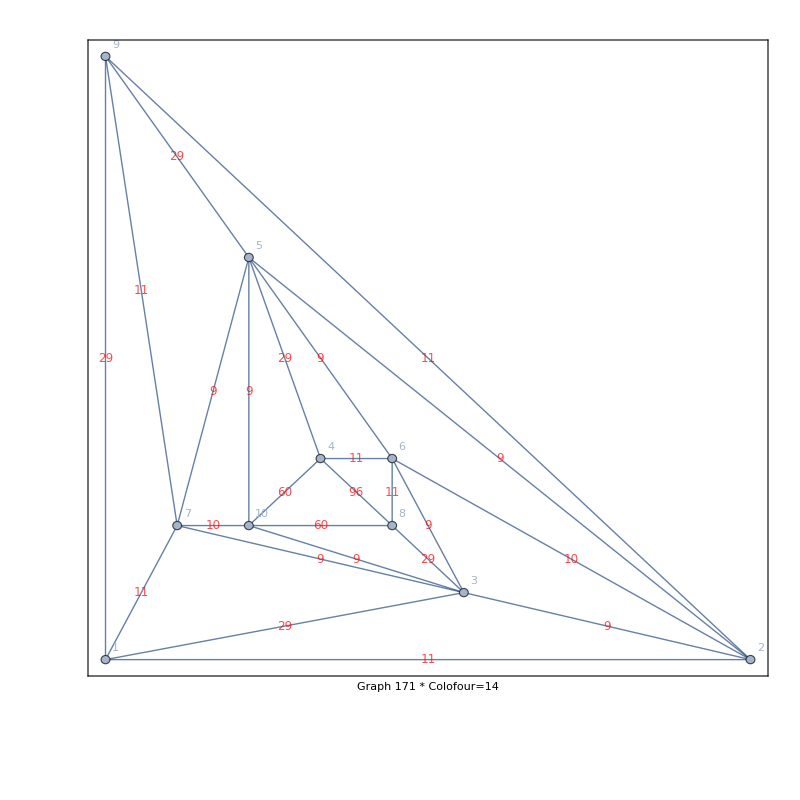

```mathematica
With[
{gn=171, val=values171},
With[{g=ReadGrof[gn]},
Graph[ReadGrof[gn],VertexLabels->"Name",EdgeLabelStyle->Directive[Red,Italic,12],GraphLayout->"PlanarEmbedding",Frame->True,FrameLabel->"Graph "<>ToString[gn]<> " * Colofour=" <> ToString[Chrom[gn]/24], ImageSize->800,EdgeLabels->Table[e->ChromaticPolynomial[Rule2[g,e,OtherEdge[g,e]],4]/24,{e,EdgeList[g]}]]
]
]
```

```mathematica
ChromaticPolynomial[Rule2[ReadGrof[171],6<->5,2<->4],4]/24
```

9

```mathematica
Reverse[2<->7]
```

7<->2

```mathematica
Graph[LineGraph[ReadGrof[171]],GraphLayout->"PlanarEmbedding"]
```

Part::partw: Part 2 of {3} does not exist.

Part::partw: Part 2 of {2} does not exist.

Part::partw: Part 2 of {1} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

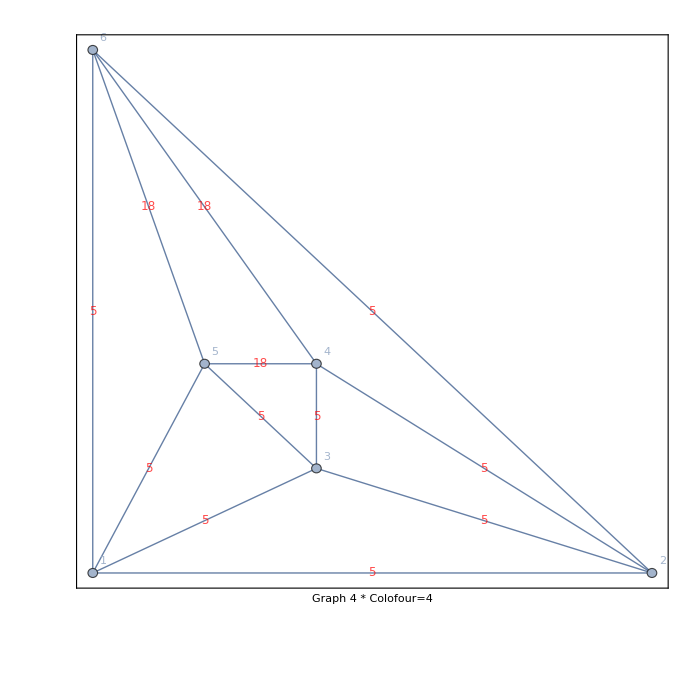

```mathematica
With[
{gn=4},
With[{g=ReadGrof[gn]},
Graph[ReadGrof[gn],VertexLabels->"Name",EdgeLabelStyle->Directive[Red,Italic,12],GraphLayout->"PlanarEmbedding",Frame->True,FrameLabel->"Graph "<>ToString[gn]<> " * Colofour=" <> ToString[Chrom[gn]/24], ImageSize->800,EdgeLabels->Table[e->ChromaticPolynomial[Rule2[g,e,OtherEdge[g,e]],4]/24,{e,EdgeList[g]}]]
]
]
```